```mathematica
img=Import["/home/kamano/TEST_COLLECTION/ChemicalStructureRecognition/cal.png"]
```

-Graphics-

```mathematica
imgG=ColorConvert[img,"Grayscale"]
```

-Graphics-

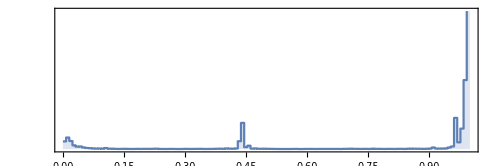

```mathematica
ImageHistogram[imgG]
```

```mathematica
imgB=Binarize[imgG]
```

-Graphics-

```mathematica
ImageValuePositions[imgB,1]//Length
```

180715

```mathematica
ImageValuePositions[imgB,0]//Length
```

30612

```mathematica
imgNg=ColorNegate[imgB]
```

-Graphics-

```mathematica
imgExLine=ImageLines[imgNg]
```

{Line[{{0.,201.001},{527.,201.001}}],Line[{{0.,75.771},{527.,75.771}}],Line[{{0.,12.6551},{527.,12.6551}}],Line[{{0.,138.887},{527.,138.887}}],Line[{{0.,264.117},{527.,264.117}}],Line[{{0.,327.233},{527.,327.233}}],Line[{{0.,390.349},{527.,390.349}}],Line[{{444.76,401.},{443.905,0.}}],Line[{{372.627,401.},{371.773,0.}}],Line[{{228.362,401.},{227.507,0.}}],Line[{{156.229,401.},{155.375,0.}}],Line[{{84.0967,401.},{83.242,0.}}],Line[{{516.892,401.},{516.038,0.}}],Line[{{300.495,401.},{299.64,0.}}],Line[{{12.9659,401.},{12.1113,0.}}],Line[{{0.,90.7986},{527.,90.7986}}],Line[{{0.,116.846},{527.,116.846}}],Line[{{0.,5.57541},{458.314,401.}}],Line[{{0.,372.961},{527.,361.727}}],Line[{{0.,357.347},{527.,339.368}}]}

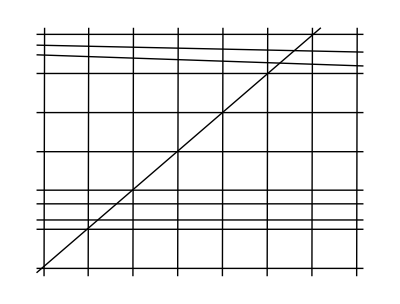

```mathematica
Graphics[imgExLine]
```